## Wolfram作为经典编程语言

## 关系运算与逻辑运算符

### 关系运算符

```mathematica
{1<Sin[1],1>Sin[1],1==Sin[1],1!=Sin[1],1<=Min[1,Sin[1]],1>=Min[1,Sin[1]],1===1.0,1=!=1.0}
```

{False,True,False,True,False,True,False,True}

```mathematica
{1∈Integers,1.01∈Integers, Pi ∈Reals, Pi ∈ Rationals, 2+3I∈ Complexes,MemberQ[{1,3,5},PrimePi[2]],MemberQ[{1,3,5},PrimePi[4]]}
```

{True,False,True,False,True,True,False}

```mathematica
{Boole[True],Boole[False],BooleanQ[True],BooleanQ[1]}
```

{1,0,True,False}

### 逻辑运算符

```mathematica
ClearAll["Global`*"]
{p,q,r}={False,True,True};
{p&&q,p ∧q, p||q,p ∨ q, !p, ¬ p}
```

{False,False,True,True,True,True}

```mathematica
{Xor[p,q],p⊻ q, Xnor[p,q],p \[Xnor] q, Nand[p,q],p ⊼ q, Nor[p,q],p ⊽ q, Implies[p,q],p ⇒ q, Equivalent[p,q],p ⧦ q}
```

{True,True,False,False,True,True,False,False,True,True,False,False}

## 条件判断

模拟掷骰子

```mathematica
rollDie[]:=Module[{result},result=RandomInteger[{1,6}];
If[result==1,Print["You rolled a 1, what a bad start!"],If[result==6,Print["You rolled a 6, what a lucky start!"],Print["You rolled a ",result,", keep going!"]]]]
rollDie[]  (*Call the function to simulate rolling a die*)
```

You rolled a 5, keep going!

扩展绝对值函数到复数(模长)

```mathematica
abs[x_]:=If[x>0,x,-x,Sqrt[Re[x]^2+Im[x]^2]]
Print[{abs[-3],abs[3.14],abs[3+4I]}]
```

Greater::nord: 尝试使用 3+4 ⅈ 进行无效的比较.

{3,3.14,5}

将截断

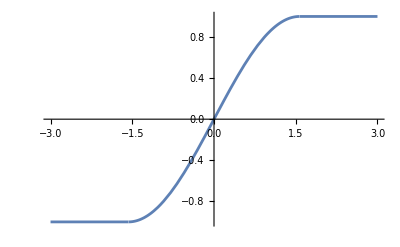

```mathematica
unitSin[x_]:=Which[x<-Pi/2,-1,x>Pi/2,1,True,Sin[x]]
Plot[unitSin[x],{x,-3,3}]
```

```mathematica
unitSin[x_]:=Piecewise[{{-1,x<-Pi/2},{1,x>Pi/2}},Sin[x]]
Plot[unitSin[x],{x,-3,3}]
```

-Graphics-

模拟猜数游戏

```mathematica
numberGuessingGame[]:=Module[{target=RandomInteger[{1,100}],guess,difference},Print["Welcome to the Number Guessing Game! Guess a number between 1 and 100."];
While[True,guess=Input["Enter your guess: "];
difference=Abs[target-guess];
Which[difference==0,Print["Congratulations! You've guessed the right number: ",target,"!"];
(*Exit the loop when guessed correctly*)Break[],difference<=5,Print["Very close! You're within 5."],difference<=15,Print["Close! You're within 15."],difference<=30,Print["Not too far! You're within 30."],True,Print["Way off! Try again!"]];]]
(*Start the game*)
numberGuessingGame[]
```

Welcome to the Number Guessing Game! Guess a number between 1 and 100.

Very close! You're within 5.

Close! You're within 15.

Congratulations! You've guessed the right number: 45!

给出动物的特性

```mathematica
animal="Dog";
description=Switch[animal,"Dog","A dog is a loyal companion.",
"Cat","A cat is independent and curious.",
"Bird","A bird can sing and fly.",
_,"Unknown animal."]
```

A dog is a loyal companion.

## 循环编程

Do循环：根据公式计算的近似值

```mathematica
apprxPi[eps_]:=Module[{n=Floor[1/eps],i,sum=0.0,sign=1},
For[i=1,i<=n,i+=2,
sum+=sign/i;
sign=-sign;
];
N[NumberForm[4.0*sum,Floor[Log10[n]]+1]]
]
apprxPi[10^-6]
```

3.141591

While循环：计算一个十进制数的进制表示

```mathematica
positiveIntegerQ[n_]:=n∈ PositiveIntegers
positiveIntegerQ/@{-1,0,3}
toPnary[num_?positiveIntegerQ,p_?positiveIntegerQ]:=Module[{i,bin={},r=num},
While[r>0,
i=Mod[r,p];
bin=Prepend[bin,i];
r=Floor[r/p];
];
bin]
toPnary[9,2]
```

{False,False,True}

{1,0,0,1}

辗转相除法求最大公约数

```mathematica
gcd[m_,n_]:=Module[{r=m,s=n,t},
While[s!=0,
(*Print[{r,s}];*)
t=Mod[r,s];
r=s;
s=t;
];
r]
gcd[10,8]
```

2

NestWhile嵌套循环列表：求正整数的下一个素数。

```mathematica
positiveIntegerQ[n_]:=n∈ PositiveIntegers
nextPrime[n_?positiveIntegerQ]:=NestWhile[#+1&,n+1,!PrimeQ[#]&]
nextPrime/@{5,9,888}
```

{7,11,907}

猫映射：天才数学家Arnold提出一种映射，对, 以及任意的, 若定义

可以证明，该映射一定是周期的。

{{2,3},{11,5},{11,7},{2,6},{5,11},{8,7},{14,0},{14,8},{8,4},{5,9},{2,8},{11,10},{11,12},{2,11},{5,1},{8,12},{14,5},{14,13},{8,9},{5,14},{2,13},{11,0},{11,2},{2,1},{5,6},{8,2},{14,10},{14,3},{8,14},{5,4},{2,3}}

{{1},{31}}

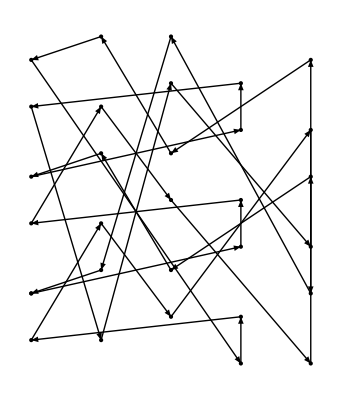

```mathematica
positiveIntegerQ[n_]:=n∈ PositiveIntegers
catMap[{x0_?positiveIntegerQ,y0_?positiveIntegerQ},{a_?positiveIntegerQ,b_?positiveIntegerQ},n_?positiveIntegerQ]:=Module[
{max=1},
NestWhileList[Mod[{#[[1]]+a #[[2]],b #[[1]]+(a b+1)#[[2]]},n]&,{x0,y0},max++<31&]
]
catMapList=catMap[{2,3},{3,7},15]
Position[catMapList,{2,3}]
Graphics[{{PointSize[Large],Point[catMapList]},Map[Arrow,Partition[catMapList,2,1]]}]
```